# On-chip verification/benchmarking procedures

## Author: Cica Gustiani (cicagustiani@gmail.com)

QuESTlink setup: set the main directory as the current directory, load questlik package, and download the link binary file.
Requirement: MOSEK lisence

```mathematica
Environment["MOSEKLM_LICENSE_FILE"]
```

:/home/cica/mosek/mosek.lic

```mathematica
SetDirectory[NotebookDirectory[]];
Quiet@Import["https://raw.githubusercontent.com/QTechTheory/QuESTlink/refs/heads/main/Link/QuESTlink.m"];
Import["https://raw.githubusercontent.com/QTechTheory/VQD/refs/heads/master/vqd.wl"];
CreateDownloadedQuESTEnv[];
Get["QuESTLinkConvention.wl"];
```

## Secret dependency in the single-qubit states preparation

### Single qubit tomography: reconstruct the single-qubit density matrix

Here, we perform tomography on the single  qubits.  
The reason behind this is XY-plane excessively need Rz-rotations, which is commonly performed in virtual manner. [Q: why does it matter? if the computation performed on the XY plane ends up performing better? how does it impact security?]. On the other hand, information in the YZ  plane encoded physically, e.g., between two energy levels.
We choose YZ instead of XZ because the circuits are much simpler.
ρ =1/2( I + r . σ), where r = (r_x, r_y, r_z) is the Bloch vector, and σ  = (X, Y, Z) is the set of Pauli operators.
Which,  r_σ= ⟨σ⟩,  is obtained by Pauli measurements. Thus, 
ρ = (1+r_z | r_x-ⅈ r_y
r_x+ⅈ r_y | 1-r_z)

### Secret dependency test

The choice of choi-representation:
A Choi matrix Λ = (I ⊗ E ) is a quantum channel if:
1) E is Hermitian-perserving ⇔ Λ^† = Λ                           (HP)
2) E is Trace-perserving ⇔ Tr_Y(Λ) = Identity                 (TP)
3) E is Complete-positive⇔ Λ ≥ 0                                      (CP)

```mathematica
ClearAll[hermitianTemplate]
hermitianTemplate::usage="hermitianTemplate[dim, variable(or {diag, real, imag}), [init_matrix]]. 
Create template for hermitian matrix. Returns {hermitian template, elements, elements_constraints, initial values} with initial value as unnormalized bell state |00>+|11>. Note that the resulting hermitian operator is in choi form.";
hermitianTemplate[n_, var_Symbol] := 
	Module[{hmat, elems, initvals, symbols, elemconst, initmat},
		hmat = Array[Subscript[var, ##]&, {n, n}];
	
		elemconst = Table[ 0 <= Subscript[var, i,i]<= 1 ,{i, n}];
		Table[
			Table[
			hmat[[col, row]] = Conjugate[Subscript[var, row, col]];
			AppendTo[elemconst, Abs[Subscript[var, row,col]] <= 1]
			,{col, row+1, n}],
		 {row, n}];
		 
		 (* identity matrix as initial value; aka bell state *)
		initmat = columnShuffle[IdentityMatrix[4]];
		initvals = Table[ hmat[[i,i]] -> initmat[[i,i]], {i, n}]; 
		Table[Table[ AppendTo[initvals, hmat[[row, col]] -> initmat[[row, col]] + 0  ⅈ], {col, row+1, n}], {row, n}];
		 
		elems = Flatten[
			{(Subscript[var, #,#] ∈ Reals)& /@ Range[n], Table[Table[Subscript[var, row,col] ∈ Complexes, {col, row+1, n}], {row, n}]}
			];
		(* the template and assumptions *)	
		{hmat, elems, elemconst, initvals}
	]
	
	hermitianTemplate[n_, var_List] := Module[{d, a, z, superop, elemconst, initval, elems},
		{d, a, z} = var;
		(* symbolic superoperator *)
		superop = DiagonalMatrix[Array[Subscript[d, #,#]&, {n}]];
		Table[
			superop[[r, c]] = Subscript[a, r,c] + ⅈ Subscript[z, r,c];
			superop[[c, r]] = Subscript[a, r,c] - ⅈ Subscript[z, r,c]
			,{r, n}, {c, r+1, n}];
			
		(* elements *)
		elems = Flatten @ {Table[Subscript[d, i,i] ∈ Reals, {i, n}],
					Table[{Subscript[a, r,c] ∈ Reals, Subscript[z, r,c]  ∈ Reals}, {r, n}, {c, r + 1, n}]};
		
		(* constraint on each element *)
		elemconst = Flatten[
			{ 
			(* diagonal constraint is probability value *)
			(0 <= Subscript[d, #,#] <= 1)& /@ Range[n], 
			(* off-diagonal constraint is complex disk with radius 1 *)
			Table[Table[
				Sqrt[Subscript[a, row, col]^2 + Subscript[z, row, col]^2] <= 1
				, {col, row + 1, n}], {row, n}]
			}
			];
		(* initial value as an identity matrix *)
		initval = Association @ Flatten[
			{ 
			Subscript[d, #, #] -> 0 &  /@ Range[n], 
			Table[Table[Subscript[a, row, col] -> 0, {col, row + 1, n}], {row, n}],
			Table[Table[Subscript[z, row, col] -> 0, {col, row + 1, n}], {row, n}]
			}
			];
		initval[Subscript[d, 1,1]]=1;
		initval[Subscript[d, 4,4]]=1;
		initval[Subscript[a, 1,4]]=1;

		{superop, elems, elemconst, Normal @ initval}		
	]
	
	costFr::usage = "costFr[results, choi_operator, elements_assumptions]. Return the cost to calculate secret dependency by using the Frobenious norm.
		1/8∑_(j = 1,  ... , 8)  1/2Tr |Ε(TemplateBox[{RowBox[{\"+\", SubscriptBox[\"θ\", \"j\"]}]},\"Ket\"])-ρ_tomo_j|_1 , where E=CPTP map tempalte, results = {{θ, ρθ_ideal, ρθ_tomography}, ... }
	";
	
	costFr[results_, choiop_, elems_:{}] := Module[{param, ρideal, ρtomo},
		Simplify[N @ ExpandAll[ 1/8*Total @ Table[
		{param, ρideal, ρtomo} = res;
		Norm[ρtomo - choiOperate[choiop, ρideal], "Frobenius"]		
		,{res, results}]], elems]
	]
	
	ClearAll[secretDependency]
	secretDependency::error="`1`";
	Options[secretDependency] = {Method -> "convex" , Chop -> False, Options -> {}};
	secretDependency::usage = "secretDependency[result_from_tomo8, Method-> `convex`,`numeric`, `idstart`, Options -> {optimization_options for ConvexOptimization, NMinimize, or FindMinimum}]. Perform optimisation to calculate secret dependency
	min_E  1/8∑_(j = 1,  ... , 8) |Ε(TemplateBox[{RowBox[{\"+\", SubscriptBox[\"θ\", \"j\"]}]},\"Ket\"])-ρ_tomo_j|_1
	output : {score_from_optimization, score_for_identity_channel, error_channel}";
	secretDependency[restomo8_, OptionsPattern[]] := Module[
	{choiop, elems, cost, xrpt, xrpt2, sol, idcost, initval, initval2, elemconst, d, a, z, method, options},
	(* loose bound, given Ε = Id *)
	
	(*idcost = 1/8 Total @ Table[Norm[res[[2]] - res[[3]], "Frobenius"],{res, restomo8}];*)
	
	
	{choiop , elems, elemconst, initval} = hermitianTemplate[4, {d,a,z}];
	options = OptionValue[Options];
	
	(* cost *)
	idcost = costFr[restomo8, choiop /. initval, elems];
	
	If[ ¬Simplify[ConjugateTranspose[choiop], elems] === choiop, 
		Throw[Message[secretDependency::error, "Template is non Hermitian"]; $Failed]
	  ];
	
	(* cost function *)
	cost = costFr[restomo8, choiop, elems];
	
	method = OptionValue[Method];
	(* restriction *)
	xrpt = (TensorContract[ArrayReshape[choiop, {2, 2, 2, 2}], {1, 3}] == IdentityMatrix[2]);
	xrpt2 = (TensorContract[ArrayReshape[choiop, {2, 2, 2, 2}], {2, 4}] == IdentityMatrix[2]);
	
	sol = Which[
		method == "convex",
		 ConvexOptimization[cost, {VectorGreaterEqual[{choiop, 0}, {"SemidefiniteCone", 4}], xrpt},
		elems, Sequence@@options, PerformanceGoal-> "Quality", MaxIterations->10^15, Method->"MOSEK"]
		,
		method == "numeric"
		,
		NMinimize[{cost, VectorGreaterEqual[{choiop, 0}, {"SemidefiniteCone", 4}], xrpt}, elems, Sequence@@options][[2]]
		,
		method == "idstart"
		,
		initval2 = (initval /. Rule -> List);
		FindMinimum[{cost,  VectorGreaterEqual[{choiop, 0}, {"SemidefiniteCone", 4}], xrpt, elemconst}, initval2][[2]]
		,
		True,
		Throw[Message[secretDependency::error, "Unkown Methode, pick one among:  `convex`,`numeric`, `idstart`"]; $Failed]	
	];
	{cost /. sol, idcost, choiop /. sol}

	]
```

```mathematica
singleQTomography::usage = "singleQTomography[data]. Estimate single density matrix from Pauli measurements. Argument data has format of  <|``X`` -> <|0->p0, 1->p1|>, ``Y``-> .. ``Z``->.. |>";
keyCheck[ass_, key_] := If[KeyExistsQ[ass, key], ass[key], 0]
singleQTomography[data_]:= Module[
	{rx, ry, rz, norm}
	, 
	rz =.5(keyCheck[data["Z"], 0] - keyCheck[data["Z"], 1]);
	rx =.5(keyCheck[data["X"], 0] - keyCheck[data["X"], 1]);
	ry =.5(keyCheck[data["Y"], 0] - keyCheck[data["Y"], 1]);
	norm = Norm[{rz, rx, ry}, 2];
	rz = rz/norm;
	ry = ry/norm;
	rx = rx/norm;
	.5{{1 + rz, rx - ⅈ ry},{rx + ⅈ ry, 1 - rz}}
]

fidSingle[ρmat_, state_] := Re[ Conjugate[state] . ρmat . state ]
```

```mathematica
(* format single-qubit measurement counts *)
Clear[formatSCounts]
formatSCounts[countl_]:=With[
	{nshot = If[ListQ@countl, 
	Total @ countl[[All, 2]], Total @ Values @ countl], 
	counts = If[ListQ @ countl, Association @ countl, countl]
	}
, 
	<| 0 -> If[KeyExistsQ[counts,"(0,)"], N[counts["(0,)"]/nshot], 0], 
	1 -> If[KeyExistsQ[counts,"(1,)"], N[counts["(1,)"]/nshot], 0]|>
	]
jsonList2Assoc[data_List]:=Table[ Association @ (entry//. {Rule[a_, b_List]:>Rule[a, Association @ b]}) ,{entry, data}]
```

```mathematica
pauli = Association[ToString@ # -> CalcCircuitMatrix[Subscript[#, 0]]& /@ {X,Y,Z}];

Clear[format2Tomo]
format2Tomo[results_List] := Module[{resultsSorted, param, list, pauli, expv, expres, ρexp, plane, ψideal, θ, desc},
	resultsSorted = SortBy[Table[res /. a_List :> Association @ a,{res, DeleteDuplicatesBy[results, #["handle"]&]}], #["description"]["angle"]&];
	pauli = Association[ ToString[#] -> CalcCircuitMatrix[Subscript[#, 0]]& /@ {X, Y, Z}];
	expres = Table[
		param = angle/4;
		list = Select[resultsSorted, #["description"]["angle"] == param & ];
		expres = Association @ Table[
			res["description"]["basis_measure"] -> formatSCounts @ res["counts"]
		,{res, list}];
	ρexp = singleQTomography @ expres ;
	plane = First[list]["description"]["basis_prepare"];
	ψideal = If[plane == "XY", {1/(√2),ⅇ^(ⅈ*θ)/(√2)}, {Cos[θ/2],-ⅈ Sin[θ/2]}] /. θ -> param * π;
	{param * π, KroneckerProduct[ψideal, Conjugate @ ψideal], ρexp}	
	, {angle, 0, 7}]

]
```

## Execute!

Secret dependency test on the experiment data

```mathematica
test1 = Association /@ Import["data/qc_tomography_YZ.json"];
sdExp = format2Tomo @ test1;
```

```mathematica
secretDependency[sdExp, Method -> "convex",Options->{Tolerance->10^(-16)}][[1;;2]]
secretDependency[sdExp, Method -> "numeric"][[1;;2]]
secretDependency[sdExp, Method -> "idstart"][[1;;2]]
```

{0.015028,0.015607}

{0.015028,0.015607}

{0.015028,0.015607}

Fideliy results on the tomography

```mathematica
infid=Table[{param,ρid,ρt}=exp;
{param,1- CalcFidelityDensityMatrices[ρid,ρt]}
,{exp, sdExp}];
```

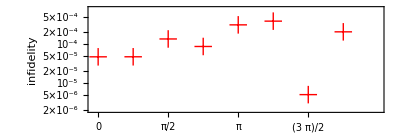

```mathematica
infidplot=ListLogPlot[infid, Frame->True,PlotMarkers->Style["+", {Bold,Red, FontSize->18}],BaseStyle->{FontFamily->"Times",FontSize->12},Axes->False,PlotRange->{{-0.1,2π},{2*10^-6,8*10^-4}},FrameStyle->Black,
FrameTicks->{{Automatic,Automatic},{{0,π/4,π/2,3π/4,π,5π/4,6π/4,7π/4},Automatic}},GridLines->{None,Automatic},GridLinesStyle->Directive[Dotted, Black],FrameLabel->{Style["θ",{FontSize->15}],Style["infidelity",{Italic,FontSize->13}]},AspectRatio->1/3]
```

```mathematica
1-Mean@infid[[All,2]]
```

0.999848